8.02 Mathematica Lesson 1
"Open/Close CoSet"

Click Enable Dynamics  in the right upper corner of the notebook before starting to work!

After reading this Mathematica notebook, you will be able to: 1)  apply basic operations of the Wolfram Language to calculate  the electric field produced by a point charge, 2) use graphing functions to visualize the electric field of a point charge, and 3) write a function using the Wolfram Language. 

Tutorial: The first part of this notebook, from section 1-R1 to 1-R5 (the brown boxes), is a tutorial. Reading the tutorial and interacting with the pieces of code in it will prepare you to do the problems at the end of this notebook.

Assignment: In the green boxes, you will find the Mathematica assignments. In the first problem, 1-P1, you will calculate and visualize the electric field of a dipole, and in the second problem, 1-P2, which is optional, you will study the electric field of the water molecule.  

Save my work: After typing one or several lines of code in your solution you can click “Save my work and Give Feedback”. “Save my work” does NOT save the changes done in the notebook. It locks your answer into the notebook by creating gray cells that can not be edited anymore. If you are not pleased with your answer you will be able to type a new solution as many times as you want.  

Access Solution: Note that after clicking “Save my work and Give Feedback” for the first time you will be able to view the solution.  This is done for pedagogical purposes. There are many ways of writing a code so the posted solution might be different from yours. 

Save: Before closing the notebook make sure that you have saved your changes by clicking Save from the File menu. If you do not save the changes the grader will not see your work and you will not receive a grade.  (Saving a file frequently is always  a good practice!)

modifying options

(*we probably won't need these*)
(*r=1.7;
radius = .04(*.4*);
inradius = .05;
radiusTWO = .1;
outerchg =2;*)
Clear[x,y,z];
Clear[PointChargeAtOriginField,x,y,z,charg];

(*changing default options for ContourPlot3D. We could even modify the d.v.'s i*)
Unprotect[ContourPlot3D];
Options[ContourPlot3D]=
{
	(*modified options*)
	PlotPoints→(*17*)26,(*Mesh→All,*)MaxRecursion→0,Mesh→None,
	ColorFunction→"TemperatureMap",ViewPoint→{1.3,-2.4,-31.}(*need to use ViewMatrix*),Contours→Range[-7,7],
	
	(*original options*)
	AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,1},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourStyle→GrayLevel[1],ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&,#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→"Fit",SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision
};
Protect[ContourPlot3D];

Unprotect[ContourPlot];
Options[ContourPlot]=
{
	(*modified options*)
	ContourLabels→True,Contours→16,
	
	(*original options*)
	Sequence@@Options[ContourPlot]
};
Protect[ContourPlot];

(*Unprotect[SliceVectorPlot3D];
Options[SliceVectorPlot3D]=
{
	(*original options*)
	Sequence@@Options[SliceVectorPlot3D],
	
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{.1,.1,-10},VectorScale→{Medium, 0.6, (*Sqrt@*)Sqrt[#5]&(*Automatic*)},(*Boxed→False,*)
	Axes→True, PlotStyle→Opacity[0.1],VectorPoints→17(*RandomReal[{-2,2},{2,888}]*),AxesLabel→Automatic
};
Protect[SliceVectorPlot3D];*)
SetOptions[SliceVectorPlot3D,ViewPoint→{.1,.1,10}];
SetOptions[SliceVectorPlot3D,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}];
SetOptions[SliceVectorPlot3D,Axes→True];
SetOptions[SliceVectorPlot3D,PlotStyle→Opacity[0.1]];
SetOptions[SliceVectorPlot3D,VectorPoints→16];
SetOptions[SliceVectorPlot3D,AxesLabel→Automatic];
SetOptions[SliceVectorPlot3D,ImageSize→Large];
SetOptions[SliceVectorPlot3D,VectorStyle→Arrowheads[.01]];

SetOptions[VectorPlot,VectorStyle→Arrowheads[.02]];
SetOptions[VectorPlot,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2)^.3&(*Automatic*)}];
SetOptions[VectorPlot,VectorPoints→16];

Unprotect[VectorPlot3D];
Options[VectorPlot3D]=
{
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{11,-20,4}(*need to use ViewMatrix!*),VectorScale→{Automatic,Automatic,Function[If[1/(#1^2+#2^2+#3^2)>2,None,1/(#1^2+#2^2+#3^2)]]}(*{Small, .6, (*Sqrt@*)(*1/*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}*),(*Boxed→False,*)
Axes→True, (*PlotStyle→Opacity[0.3],*)VectorPoints→10(*RandomReal[{-2,2},{2,888}]*),AxesLabel→{"x","y","z"},
	(*original options*)
	Sequence@@Options[VectorPlot3D]
};
Protect[VectorPlot3D];
SetOptions[VectorPlot3D,ImageSize→Large];

Clear[x,y,z];

Electric fields due to point charges 
"Open/Close Chapter"

Writing the 3-components of the electric field in the Wolfram Language.
"Open/Close Section"

This point marks the beginning of the first accompanying video lesson

In the white box below you will see a piece of code that assigns the numerical value 2*10^-9 C to the variable “charge”. Throughout the semester we will consistently use SI units but in our code we will suppress the units and indicate them in a comment. To write a comment in a code we use the parenthesis and the asterisk (*  *) as shown below:

charge = 2*10^(-9)  (* Units [charge] = C *)

1/500000000

For the rest of the notebook, charge is set to the value assigned above.

The next line of code assigns the value of  9*10^9 N.C^-2.m^2  to the Coulomb constant.

k = 9*10^9     (* Units [k] = N.C^2/m^2 *)

9000000000

We will call the location of the point charge “sourcePoint”, and the point where we want to measure the electric field “fieldPoint”. These will be represented by (3-dimensional) vectors. In the Wolfram language a 3D vector is a list with three numbers. A list is indicated with curly brackets as shown below:

sourcePoint = {0,0,0};   (* the charge is at the origin in meters*)
fieldPoint={x,y,z};(* position of point P in meters*)

The electric field is given by (k* charge* (fieldPoint - sourcePoint))/(|fieldPoint- sourcePoint|^3),

where |fieldPoint- sourcePoint| = | (r⃗)_P-(r⃗)_s| is the distance between point P and the source charge, as shown in the diagram below:

-Graphics-


In the Wolfram Language, the distance between two points can be found using either Norm[ ] or EuclideanDistance[ ], so, we can express our electric field as follows:

eField = k*charge*(fieldPoint-sourcePoint )/EuclideanDistance[fieldPoint, sourcePoint]^3

{(18 x)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(18 y)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(18 z)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

Visualizing a 3D vector field
"Open/Close Section"

We will use the graphing function VectorPlot3D[ ] to visualize an electric field. In the line below, we ask the function VectorPlot3D[ ] to draw  the electric field ‘eField’  in the region  -1 < x <1,  -1 < y <1, and -1 < z <1.  The syntax used to indicate the interval -1 < x < 1 is {x, -1, 1}. (The same is done for the y and the z axis.)

VectorPlot3D[eField,{x,-1,1},{y,-1,1},{z,-1,1}]

-Graphics3D-

Note 1: Use the mouse (click-and-drag) to rotate the figure. 
Note 2: The 3D vector field looks too messy. You can still see that all the arrows are pointing away from the origin where the positive charge is located.
Note 3: The magnitude of the electric field is inversely proportional to the square of the distance from the source point. Therefore we expect the arrows associated with the electric field to diminish quite rapidly as we move away from the source point. This is not what it is observed in the vector plot above because the lengths of the arrows have been intentionally rescaled to produce a nice visualization, especially close to the source point where the magnitude of the field approaches infinity.

Visualizing the electric field in relevant planes
"Open/Close Section"

Because of the spherical symmetry of the electric field produced by a point charge, any plane containing the charge will present the same electric field pattern. We will consider three orthogonal planes containing the charge and we will use another graphing function, SliceVectorPlot3D[ ], to visualize the electric field on these planes.

SliceVectorPlot3D[eField, "CenterPlanes",{x,-1,1},{y,-1,1},{z,-1,1},VectorStyle→Arrowheads[.01]]

-Graphics3D-

Use the mouse (click-and-drag) to rotate the figure. 

We can see that the electric field pattern is identical in the three planes. The spherical symmetry of the field allows us to use any plane containing the charge to describe the electric field completely. In this example of a field produced by a positive charge, the electric field is characterized by arrows starting at the origin and pointing radially outwards.

VectorStyle is an option to use with the graphing function SliceVectorPlot3D[ ] that determines the style to use for drawing  vectors. To have a nice picture of the electric field vectors in the plot above, we set the size of the arrows using VectorStyle→Arrowheads[.01] (set the arrowheads to have a length that is a fraction 0.01 of the total width of the graphic).

You are encouraged to change the size of the arrows, style, color, etc to improve the plot. For more information, click “Help” in the bar menu, select “Wolfram Documentation”, and type “VectorStyle”. It is amazing how much you will learn from the help sections.

If the charge at the origin is a negative charge, the arrows will be pointing radially towards the origin, but the picture will otherwise be the same. In the line of code below  we plot ‘-eField’, which is algebraically the same as replacing ‘charge’ with ‘-charge’:

SliceVectorPlot3D[-eField, "CenterPlanes",{x,-1,1},{y,-1,1},{z,-1,1},VectorStyle→Arrowheads[.01]]

-Graphics3D-

You can specify which plane(s) you wish to use to slice the electric field by typing a list {...} of equation(s) of planes into the second argument of SliceVectorPlot3D[ ].  If we want to see the electric field vectors on a plane that does not contain the charge, for example the plane at z = 0.2, we type:

SliceVectorPlot3D[eField, {z==0.2},{x,-1,1},{y,-1,1},{z,-1,1},VectorStyle→Arrowheads[.01]]

-Graphics3D-

Use the mouse to rotate the plot above. The electric field at any point in the z = 0.2 plane has a non zero z-component (component perpendicular to the plane). In contrast, at any point in the  z = 0 plane the z-component of the electric field is zero (use z = 0 in  SliceVectorPlot3D[ ] to compare).  

Because of the spherical symmetry, the electric field at any point on a plane containing the charge does not have a component perpendicular to the plane.

Visualizing the electric field in the (x,y) plane
"Open/Close Section"

In this section we present two new visualization functions: VectorPlot[ ] and StreamPlot[ ]. These functions are used to plot 2D fields. 

For a positive point charge located at the origin, we use this function to plot the electric field in the z = 0 plane. In the next 3 lines of code we calculate “eField2D”, the mathematical expression of the 2D electric field in the z = 0 plane.

sourcePoint2D = {0,0};   (* the charge is at the origin *)          
fieldPoint2D={x,y};(* point P in the x-y plane*)

eField2D = k*charge*(fieldPoint2D-sourcePoint2D )/EuclideanDistance[fieldPoint2D, sourcePoint2D]^3

{(18 x)/((Abs[x]^2+Abs[y]^2)^(3/2)),(18 y)/((Abs[x]^2+Abs[y]^2)^(3/2))}

Now that we have a 2D vector field, we can use 2D plotting tools:

VectorPlot[eField2D,{x,-2,2},{y,-2,2}]

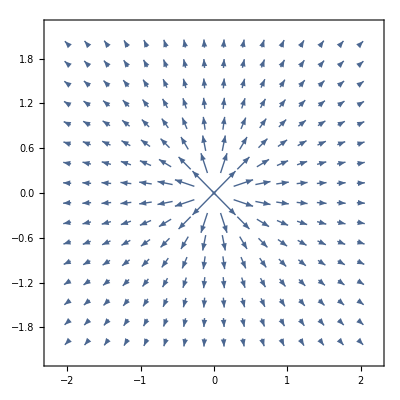

Up to now we have represented the electric field by a collection of vectors in space. Sometimes we will use electric field lines to describe the electric field. The streamlines are the lines that are tangent to the electric field vectors. In the line of code below we use the Mathematica function StreamPlot[...] to plot the electric field lines:

StreamPlot[eField2D,{x,-2,2},{y,-2,2}]

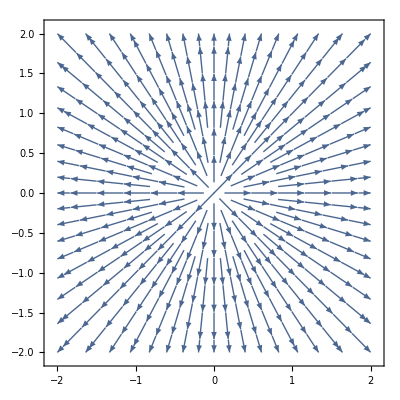

This point marks the end of the first accompanying video lesson and the beginning of the second video lesson.

Electric fields using Wolfram Language functions
"Open/Close Section"

Introduction to functions

To work with a set of many point charges (as well as do many other things), it is useful to know how to create a “function”: a convenient shortcut to doing something (something that may depend on what you feed into the function as inputs, or “arguments”).

The line in the box below, defines a function “f” for squaring an expression. The syntax used to indicate the argument of a function is “x_ “, the argument x is followed by an underscore inside the square brackets [ ]. The expression to be evaluated by the function is preceeded by “:=”.

f[x_]:=x^2

Now f can be used in the way any built-in function can:

f[4]

16

f[a-b]

(a-b)^2

Here’s how to create a function of two arguments:

g[x_, y_] := x^2+y^2

g[Sin[0.2Pi],Cos[0.2Pi]]

1.

For more detail about how to write functions refer to the accompanying video or this guide page.

Expressing electric field from a point charge as a function

Now we will take our expression for the field of a point charge, and define a function that returns the field at any point. 

The electric field at a point depends on 3 arguments: the value of the charge, the location of the charge, and the location at which we wish to know the field, so we need to pass these 3 arguments to our function: sourcePoint, fieldPoint, and charge:

eFieldFunc[sourcePoint_, fieldPoint_, charge_] := k*charge*(fieldPoint-sourcePoint )/EuclideanDistance[fieldPoint, sourcePoint]^3

Note again that sourcePoint, fieldPoint,  and charge are used as arguments in the function, therefore  they are followed by the underscore  “_” inside the square brackets.  Also note that the eFieldFunc[ ] that we defined takes two vectors and a scalar as input, so there are seven parameters.

Earlier we discussed the field due to a single charge of 2 10^-9 C at the origin, measured at any point (x,y,z). This electric field can be reproduced by using the function defined above with the proper arguments:

eFieldFunc[{0,0,0},{x,y,z},2 * 10^(-9)]

{(18 x)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(18 y)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(18 z)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

Note that the output of eFieldFunc[ ] in the above example is the electric field at an arbitrary point {x, y, z} . We can also calculate the electric field at a specific point in space. Example,  set the input fieldPoint = {.7 ,1.23,.89}  as shown below:

eFieldFunc[{0,0,0},{.7 ,1.23,.89},2 * 10^(-9)]

{2.69648,4.73811,3.42839}

This point marks the end of thesecond accompanying video lesson and the beginning of your assignment.

Problem 1: Electric field of a dipole
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Use the function “eFieldFunc” to calculate  the electric field of a dipole formed by a positive charge of 5x10^-9C located at x = 1 A^o (one angstrom) and a negative charge of -5x10^-9C located at x = -1 A^o .  Use VectorPlot3D[] to do the 3D visualization (the axis are in units of A^o).

A little hint
"Show hint for 0 credits"

Work saved at Mon 12 Feb 2018 17:26:12

```mathematica
dipoleCharge :=5*10^(-9) (* [dipoleCharge] = C *)
dipoleField = eFieldFunc[{1,0,0},{x,y,z}, dipoleCharge] + eFieldFunc[{-1,0,0}, {x,y,z},-dipoleCharge] (* [dipoleField] = N/C *)
```

{(45 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 (1+x))/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 y)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 z)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

```mathematica
VectorPlot3D[dipoleField, {x,-2,2}, {y,-2,2}, {z,-2,2}] (* [x],[y],[z] = angstrom *)
```

-Graphics3D-

Work saved at Mon 12 Feb 2018 17:30:22

```mathematica
dipoleCharge :=5*10^(-9) (* [dipoleCharge] = C *)
dipoleField = eFieldFunc[{1,0,0},{x,y,z}, dipoleCharge] + eFieldFunc[{-1,0,0}, {x,y,z},-dipoleCharge] (* [dipoleField] = N/C *)
```

{(45 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 (1+x))/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 y)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 z)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

```mathematica
VectorPlot3D[dipoleField, {x,-2,2}, {y,-2,2}, {z,-2,2}] (* [x],[y],[z] = angstrom *)
```

-Graphics3D-

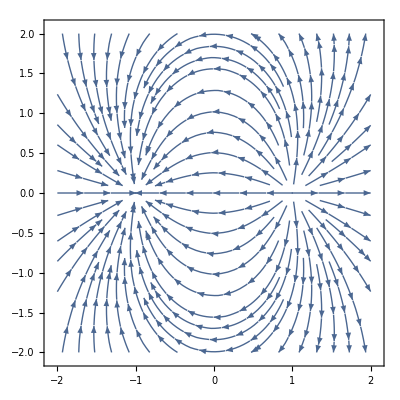

```mathematica
Block[{z=0},StreamPlot[{dipoleField[[1]],dipoleField[[2]]},{x,-2,2}, {y,-2,2}]]
```

Work saved at Mon 12 Feb 2018 17:32:44

```mathematica
dipoleCharge :=5*10^(-9) (* [dipoleCharge] = C *)
dipoleField = eFieldFunc[{1,0,0},{x,y,z}, dipoleCharge] + eFieldFunc[{-1,0,0}, {x,y,z},-dipoleCharge] (* [dipoleField] = N/C *)
```

{(45 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 (1+x))/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 y)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 z)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

```mathematica
VectorPlot3D[dipoleField, {x,-2,2}, {y,-2,2}, {z,-2,2}] (* [x],[y],[z] = angstrom *)
```

-Graphics3D-

```mathematica
Block[{z=0},StreamPlot[{dipoleField[[1]],dipoleField[[2]]},{x,-2,2}, {y,-2,2}]]
```

-Graphics-

```mathematica
SliceVectorPlot3D[dipoleField, {z==0},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle->Arrowheads[.01]]
```

-Graphics3D-

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
dipoleCharge :=5*10^(-9) (* [dipoleCharge] = C *)
dipoleField = eFieldFunc[{1,0,0},{x,y,z}, dipoleCharge] + eFieldFunc[{-1,0,0}, {x,y,z},-dipoleCharge] (* [dipoleField] = N/C *)
```

{(45 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 (1+x))/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 y)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 z)/((Abs[1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

```mathematica
VectorPlot3D[dipoleField, {x,-2,2}, {y,-2,2}, {z,-2,2}] (* [x],[y],[z] = angstrom *)
```

-Graphics3D-

```mathematica
Block[{z=0},StreamPlot[{dipoleField[[1]],dipoleField[[2]]},{x,-2,2}, {y,-2,2}]]
```

-Graphics-

```mathematica
SliceVectorPlot3D[dipoleField, {z==0},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle->Arrowheads[.01]]
```

-Graphics3D-

Problem 1 solution
"Open/Close Section""Access Solution"

The field produced by the two charges in the dipole is the (vector) sum of the fields from each charge.

Clear[x,y,z]
dipoleCharge = 5 * 10^(-9)  (* units C*)

1/200000000

dipoleField = eFieldFunc[{1,0,0},{x,y,z},dipoleCharge]+eFieldFunc[{-1,0,0}*10^(-10),{x,y,z},-dipoleCharge]
(* dipoleField units of N/C and the positions in amstrong *)

{(45 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 (1/10000000000+x))/((Abs[1/10000000000+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 y)/((Abs[1/10000000000+x]^2+Abs[y]^2+Abs[z]^2)^(3/2)),(45 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(45 z)/((Abs[1/10000000000+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))}

We can visualize vector fields using VectorPlot3D[]

VectorPlot3D[dipoleField,{x,-2,2},{y,-2,2},{z,-2,2}]
(* x,y,z axis in Aangstrom *)

-Graphics3D-

Note that again we have a symmetry: this time rotational symmetry of the electric field about the x-axis (which contains the point charges). Therefore every plane/slice that contains the x-axis must look the same. In particular, we can visualize the electric field in the z = 0 plane.  In the code below

SliceVectorPlot3D[dipoleField, {z==0},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle→Arrowheads[.007]]
(* x,y,z axis in Aangstrom *)

-Graphics3D-

If we want to visualize the electric field lines in the (x,y) plane we need the x and the y components of the electric field in the z = 0 plane to use the function StreamPlot[ ]. We can follow two approaches:

1. Calculate a new electric field as done in section 1-R4 of the tutorial, or

2. Use the x and the y components of the dipoleField calculated before evaluated at z = 0. The syntax use to obtain the x- component of the 3D vector dipoleField is: “dipoleField[[1]]”, and the y-component is “dipoleField[[2]]”.  (Even though we know the third coordinate will be 0 after setting z=0, we still have to use the x and y components of dipoleField for StreamPlot[] to work properly). The syntax is as follows:

Block[{z = 0},
StreamPlot[{dipoleField[[1]], dipoleField[[2]]},{x,-2,2},{y,-2,2}]
]

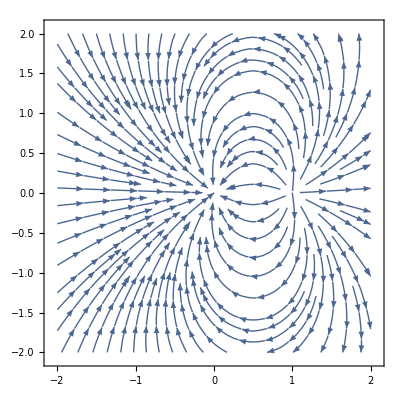

Use the button above to start viewing the solution

Optional Problem: the electric field of a water molecule
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Express and visualize the field due to a water molecule.

-Graphics-

We can represent the distribution of charge in a water molecule, H2O, by three effective point charges due to the covalent bonds between the 3 atoms: a positive charge of 0.32e on each hydrogen, and a balancing -0.64e on the oxygen atom, where e = 1.6x10^-19C is the magnitude of the charge of an electron. Additionally, these are configured in a 104° isosceles triangle with legs of 1 A^o (one angstrom), as shown in the figure above.

Work saved at Mon 12 Feb 2018 17:46:30

```mathematica
e:=1.6*10^(-19) (* [e] = C *)
```

```mathematica
oxygen :=-0.64 * e (* [oxygen] = C *)
```

```mathematica
hydrogen := 0.32 * e (* [hydrogen] = C *)
```

```mathematica
waterField = eFieldFunc[{0,0,0}, {x,y,z}, oxygen] + eFieldFunc[{1,0,0}, {x,y,z},hydrogen] + eFieldFunc[{Cos[104 Degree],Sin[104 Degree],0},{x,y,z}, hydrogen]
```

{(4.608×10^-10 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 x)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 (x+Sin[14 °]))/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2)),(4.608×10^-10 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 y)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 (y-Cos[14 °]))/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2)),(4.608×10^-10 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 z)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 z)/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2))}

```mathematica
VectorPlot3D[waterField, {x,-2,2}, {y,-2, 2}, {z, -2,2}]
```

-Graphics3D-

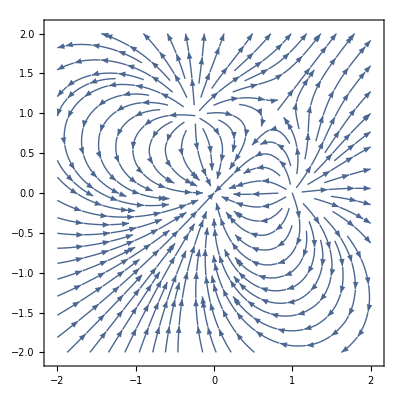

```mathematica
Block[{z=0},StreamPlot[{waterField[[1]],waterField[[2]]}, {x,-2,2},{y,-2,2}]]
```

```mathematica
SliceVectorPlot3D[waterField, {z==0.5},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle->Arrowheads[.01]]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[waterField, {z==-0.5},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle->Arrowheads[.01]]
```

-Graphics3D-

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
e:=1.6*10^(-19) (* [e] = C *)
```

```mathematica
oxygen :=-0.64 * e (* [oxygen] = C *)
```

```mathematica
hydrogen := 0.32 * e (* [hydrogen] = C *)
```

```mathematica
waterField = eFieldFunc[{0,0,0}, {x,y,z}, oxygen] + eFieldFunc[{1,0,0}, {x,y,z},hydrogen] + eFieldFunc[{Cos[104 Degree],Sin[104 Degree],0},{x,y,z}, hydrogen]
```

{(4.608×10^-10 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 x)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 (x+Sin[14 °]))/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2)),(4.608×10^-10 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 y)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 (y-Cos[14 °]))/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2)),(4.608×10^-10 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 z)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 z)/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2))}

```mathematica
VectorPlot3D[waterField, {x,-2,2}, {y,-2, 2}, {z, -2,2}]
```

-Graphics3D-

```mathematica
Block[{z=0},StreamPlot[{waterField[[1]],waterField[[2]]}, {x,-2,2},{y,-2,2}]]
```

-Graphics-

```mathematica
SliceVectorPlot3D[waterField, {z==0.5},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle->Arrowheads[.01]]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[waterField, {z==-0.5},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle->Arrowheads[.01]]
```

-Graphics3D-

solution: the field of a water molecule
"Open/Close Section""Access Solution"

Consider a coordinate system with its origin at the oxygen atom. One of the hydrogen atoms is on the x-axis. The positions of the effective charges can be found with trigonometry:

posO = {0,0,0}; (* oxygen atom at the origin *)
posH1 = {1,0,0}; (* one hydrogen atom on the x-axis -  [angstrom] *)
posH2 = {Cos[104 Degree], Sin[104 Degree], 0};(* [angstrom] *)

Let’s check posH2 looks reasonable:

posH2

{-Sin[14 °],Cos[14 °],0}

Now, using the superposition principle, we can get the water molecule’s electric field by adding three fields together:

eCharge = 1.6*10^(-19); (* magnitude of the charge of an electron - [Coulomb] *)
waterField = 
eFieldFunc[posO,{x,y,z}, -.64 * eCharge]+
eFieldFunc[posH1,{x,y,z}, .32* eCharge]+
eFieldFunc[posH2,{x,y,z}, .32* eCharge]

{(4.608×10^-10 (-1+x))/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 x)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 (x+Sin[14 °]))/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2)),(4.608×10^-10 y)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 y)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 (y-Cos[14 °]))/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2)),(4.608×10^-10 z)/((Abs[-1+x]^2+Abs[y]^2+Abs[z]^2)^(3/2))-(9.216×10^-10 z)/((Abs[x]^2+Abs[y]^2+Abs[z]^2)^(3/2))+(4.608×10^-10 z)/((Abs[z]^2+Abs[y-Cos[14 °]]^2+Abs[x+Sin[14 °]]^2)^(3/2))}

Here is the first of 3 ways to visualize the result by using SliceVectorPlot3D[]

SliceVectorPlot3D[waterField, {z==0},{x,-2,2},{y,-2,2},{z,-2,2}
, VectorStyle→Arrowheads[.01]] (* x and y axis in amstrong*)

-Graphics3D-

Here is the second way using VectorPlot3D[]

VectorPlot3D[waterField,{x,-2,2},{y,-2,2},{z,-2,2}]
(* x,y,z axis in amstrong*)

-Graphics3D-

and finally the two dimensional projection using StreamPlot[]

StreamPlot[ReplaceAll[waterField,z→0][[1;;2]],{x,-2,2},{y,-2,2}]
(* x and y axis in amstrong*)

-Graphics-

Use the button above to start viewing the solution